```mathematica
Task3AmericanPutPrices={
{0,10},{2,8},{4,6},{6,4},{8,2.12613},{10,0.955676},{12,0.387326},{14,0.143181},{16,0.0506531},{18,0.017067},{20,0.0056954}
};
Task3EuropeanPutPrices={
{0,9.60789},{2,7.60789},{4,5.60827},{6,3.64966},{8,1.99227},{10,0.913908},{12,0.375604},{14,0.139556},{16,0.049621},{18,0.0167985},{20,0.00559435}
};
```

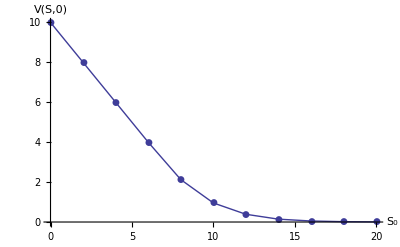

```mathematica
plotA=ListPlot[Task3AmericanPutPrices, AxesOrigin->{0,0}, Joined->True, PlotMarkers->Automatic,AxesLabel->{"S_0","V(S,0)"}]
```

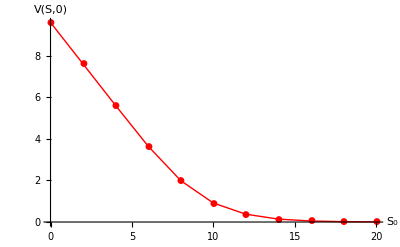

```mathematica
plotE=ListPlot[Task3EuropeanPutPrices, AxesOrigin->{0,0}, Joined->True, PlotMarkers->Automatic,PlotStyle->Red,AxesLabel->{"S_0","V(S,0)"}]
```

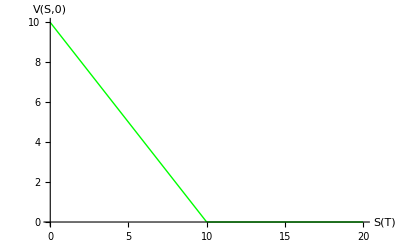

```mathematica
plotP=Plot[Max[10-ST,0],{ST,0,20},PlotStyle->Green,AxesLabel->{"S(T)","V(S,0)"}]
```

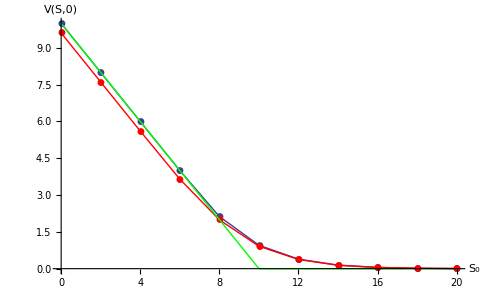

```mathematica
Show[{plotA,plotE,plotP}]
```